```mathematica
(*Scri liegt bei rho^2+z^2=Rp^2 dies soll in den Koordinaten (eta,xi) ausgeschnitten werden*)
```

## Transformation der Metrik

```mathematica
ClearAll["Global`*"]
$Assumptions=M>0&&m>0&&a0≥0&&s≥0&&ϑ≥0&&ϑ≤π/2;
𝕩3={R,ϑ,φ};
d𝕩3={dR,dϑ,dφ};
dim3=Length[𝕩3];
(*
Linienelement der 3er Metrik
R∈[0,Rp]
*)
ds2c=dR^2+R^2(dϑ^2 + Sin[ϑ]^2 dφ^2)
(*Transformation nach (ρ,z)*)
𝕩3={ρ,z,φ};
d𝕩3={dρ,dz,dφ};
dim3=Length[𝕩3];
R=Sqrt[ρ^2 + z^2];
ϑ=ArcCos[z/Sqrt[ρ^2 + z^2]];
dR=Sum[D[R,𝕩3[[ν]]] d𝕩3[[ν]],{ν,1,dim3}];
dϑ=Sum[D[ϑ,𝕩3[[ν]]] d𝕩3[[ν]],{ν,1,dim3}];
ds2c=FullSimplify[ds2c]
```

dR^2+R^2 (dϑ^2+dφ^2 Sin[ϑ]^2)

dz^2+dρ^2+dφ^2 ρ^2

```mathematica
γc=Table[(1/2+(1/2) KroneckerDelta[νν,ν]) Coefficient[ds2c,d𝕩3[[νν]] d𝕩3[[ν]]],{νν,1,dim3},{ν,1,dim3}];
γc=ParallelMap[Simplify,γc];
detγ=Simplify[Det[γc]];
γcinv=Inverse[γc];
γcinv=ParallelMap[Simplify,γcinv];
TimeUsed[]/60
Γγc=Table[Sum[1/2 γcinv[[i,l]] (D[γc[[k,l]],𝕩3[[j]]]+D[γc[[j,l]],𝕩3[[k]]]-D[γc[[j,k]],𝕩3[[l]]]),{l,1,dim3}],{i,dim3},{j,dim3},{k,dim3}];
Γγc=ParallelMap[Simplify,Γγc];
Γc=Table[Sum[γcinv[[i,j]]Γγc[[l,i,j]],{i,dim3},{j,dim3}],{l,dim3}];
Γc=ParallelMap[Simplify,Γc];
```

0.0143031

```mathematica
Laplace[Φ_]:=(1/Sqrt[detγ]) Sum[D[Sum[γcinv[[i,j]] Sqrt[detγ] D[Φ,𝕩3[[j]]],{j,1,3}],𝕩3[[i]]],{i,1,3}];
DD[Φ_,Ψ_]:=Sum[γcinv[[i,j]]D[Φ,𝕩3[[i]]]D[Ψ,𝕩3[[j]]],{i,1,dim3},{j,1,dim3}]
```

```mathematica
HamiltonConstraint=8ω[ρ,z]^2Laplace[ϕ[ρ,z]] - 8 ω[ρ,z]DD[ϕ[ρ,z],ω[ρ,z]] - (4 ω[ρ,z]Laplace[ω[ρ,z]] - 6 DD[ω[ρ,z],ω[ρ,z]])ϕ[ρ,z] - 2/3 ktr^2 ϕ[ρ,z]^5 + ω[ρ,z]^6 AA ϕ[ρ,z]^(-7);
```

```mathematica
HamiltonConstraint
```

-2/3 ktr^2 ϕ[ρ,z]^5+(AA ω[ρ,z]^6)/ϕ[ρ,z]^7-8 ω[ρ,z] (ϕ^(0,1)[ρ,z] ω^(0,1)[ρ,z]+ϕ^(1,0)[ρ,z] ω^(1,0)[ρ,z])+(8 ω[ρ,z]^2 (√(ρ^2) ϕ^(0,2)[ρ,z]+(ρ ϕ^(1,0)[ρ,z])/(√(ρ^2))+√(ρ^2) ϕ^(2,0)[ρ,z]))/(√(ρ^2))-ϕ[ρ,z] (-6 ((ω^(0,1)[ρ,z])^2+(ω^(1,0)[ρ,z])^2)+(4 ω[ρ,z] (√(ρ^2) ω^(0,2)[ρ,z]+(ρ ω^(1,0)[ρ,z])/(√(ρ^2))+√(ρ^2) ω^(2,0)[ρ,z]))/(√(ρ^2)))

```mathematica
Print["H1"];
H1=Simplify[Coefficient[HamiltonConstraint,Derivative[2,0][ϕ][ρ,z]],Assumptions:>kappa[ρ,z]≥0&&psi[ρ,z]≥0];
Print["H2"];
H2=Simplify[Coefficient[HamiltonConstraint,Derivative[0,2][ϕ][ρ,z]],Assumptions:>kappa[ρ,z]≥0&&psi[ρ,z]≥0];
Print["H3"];
H3=Simplify[Coefficient[HamiltonConstraint,Derivative[1,1][ϕ][ρ,z]],Assumptions:>kappa[ρ,z]≥0&&psi[ρ,z]≥0];
Print["H4"];
H4=Simplify[Coefficient[HamiltonConstraint,Derivative[1,0][ϕ][ρ,z]],Assumptions:>kappa[ρ,z]≥0&&psi[ρ,z]≥0];
Print["H5"];
H5=Simplify[Coefficient[HamiltonConstraint,Derivative[0,1][ϕ][ρ,z]],Assumptions:>kappa[ρ,z]≥0&&psi[ρ,z]≥0];
Print["H6"];
H6=Simplify[Coefficient[HamiltonConstraint,ϕ[ρ,z]],Assumptions:>kappa[ρ,z]≥0&&psi[ρ,z]≥0];
Print["H7"];
H7=Simplify[Coefficient[HamiltonConstraint,ϕ[ρ,z],5],Assumptions:>kappa[ρ,z]≥0&&psi[ρ,z]≥0];
Print["H8"];
H8=Simplify[Coefficient[HamiltonConstraint,ϕ[ρ,z],-7],Assumptions:>kappa[ρ,z]≥0&&psi[ρ,z]≥0];
Print["Vollständigkeitstest"];
Simplify[HamiltonConstraint - (H1 Derivative[2,0][ϕ][ρ,z] +H2 Derivative[0,2][ϕ][ρ,z]+H3 Derivative[1,1][ϕ][ρ,z] +H4 Derivative[1,0][ϕ][ρ,z] +H5 Derivative[0,1][ϕ][ρ,z]+H6 ϕ[ρ,z]+H7 ϕ[ρ,z]^5 +H8 ϕ[ρ,z]^(-7))]
```

H1

H2

H3

H4

H5

H6

H7

H8

Vollständigkeitstest

0

```mathematica
H1Test=8*ω[ρ,z]^2γcinv[[1,1]];
H2Test=8*ω[ρ,z]^2γcinv[[2,2]];
H3Test=16*ω[ρ,z]^2γcinv[[1,2]];
H4Test=-8ω[ρ,z]^2 Γc[[1]] - 8ω[ρ,z] γcinv[[1,1]] D[ω[ρ,z],𝕩3[[1]]]- 8ω[ρ,z] γcinv[[1,2]] D[ω[ρ,z],𝕩3[[2]]];
H5Test=-8ω[ρ,z]^2 Γc[[2]] - 8ω[ρ,z] γcinv[[2,1]] D[ω[ρ,z],𝕩3[[1]]]- 8ω[ρ,z] γcinv[[2,2]] D[ω[ρ,z],𝕩3[[2]]];
H6Test=-4ω[ρ,z](γcinv[[1,1]]D[ω[ρ,z],𝕩3[[1]],𝕩3[[1]]] + 2γcinv[[1,2]]D[ω[ρ,z],𝕩3[[1]],𝕩3[[2]]] + γcinv[[2,2]]D[ω[ρ,z],𝕩3[[2]],𝕩3[[2]]] - Γc[[1]]D[ω[ρ,z],𝕩3[[1]]] - Γc[[2]]D[ω[ρ,z],𝕩3[[2]]]) + 6(γcinv[[1,1]]D[ω[ρ,z],𝕩3[[1]]]^2 + 2γcinv[[1,2]]D[ω[ρ,z],𝕩3[[1]]]D[ω[ρ,z],𝕩3[[2]]]+γcinv[[2,2]]D[ω[ρ,z],𝕩3[[2]]]^2);
```

```mathematica
Simplify[H1-H1Test]
Simplify[H2-H2Test]
Simplify[H3-H3Test]
Simplify[H4-H4Test]
Simplify[H5-H5Test]
Simplify[H6-H6Test]
```

0

0

0

«3 more identical outputs»

```mathematica
ω[ρ_,z_]=(Rp^2-R^2)/(Rp^2)
```

(Rp^2-z^2-ρ^2)/Rp^2

```mathematica
Simplify[H1]
```

(8 (-Rp^2+z^2+ρ^2)^2)/Rp^4

```mathematica
Simplify[H2]
```

(8 (-Rp^2+z^2+ρ^2)^2)/Rp^4

```mathematica
Simplify[H3]
```

0

```mathematica
Simplify[H4]
```

(8 (Rp^4-2 Rp^2 z^2+z^4-ρ^4))/(Rp^4 ρ)

```mathematica
Simplify[H5]
```

-(16 z (-Rp^2+z^2+ρ^2))/Rp^4

```mathematica
FullSimplify[H6]
```

24/Rp^2

```mathematica
Simplify[H7]
```

-(2 ktr^2)/3

```mathematica
Simplify[H8]
```

(AA (-Rp^2+z^2+ρ^2)^6)/Rp^12

```mathematica
Solve[Simplify[HamiltonConstraint/.z->Sqrt[Rp^2-ρ^2]]==0,ϕ[ρ,√(Rp^2-ρ^2)]]
```

{{ϕ[ρ,√(Rp^2-ρ^2)]→0},{ϕ[ρ,√(Rp^2-ρ^2)]→-(√6)/(√ktr √Rp)},{ϕ[ρ,√(Rp^2-ρ^2)]→-(ⅈ √6)/(√ktr √Rp)},{ϕ[ρ,√(Rp^2-ρ^2)]→(ⅈ √6)/(√ktr √Rp)},{ϕ[ρ,√(Rp^2-ρ^2)]→(√6)/(√ktr √Rp)}}

```mathematica
Simplify[D[HamiltonConstraint,ρ]/.z->Sqrt[Rp^2-ρ^2]]/.ϕ[ρ,√(Rp^2-ρ^2)]->(√6)/(√ktr √Rp)/.ρ->Rp
```

-(128 ϕ^(1,0)[Rp,0])/Rp^2

```mathematica
ϕ[ρ_,z_]=(√6)/(√ktr √Rp) + ϕ11 ρ z + phi30 z^3 + phi21 z^2 ρ + phi12 z ρ^2 + phi03 ρ^3
```

(√6)/(√ktr √Rp)+phi30 z^3+phi21 z^2 ρ+phi12 z ρ^2+phi03 ρ^3+z ρ ϕ11

```mathematica
Expand[Simplify[HamiltonConstraint/.z->Sqrt[Rp^2-ρ^2]/.ρ->Rp]]
Expand[Simplify[HamiltonConstraint/.ρ->Sqrt[Rp^2-z^2]/.z->Rp]]
```

-96 phi03 Rp-40 √6 √ktr phi03^2 Rp^(9/2)-40 ktr phi03^3 Rp^8-10 √(2/3) ktr^(3/2) phi03^4 Rp^(23/2)-2/3 ktr^2 phi03^5 Rp^15

-96 phi30 Rp-40 √6 √ktr phi30^2 Rp^(9/2)-40 ktr phi30^3 Rp^8-10 √(2/3) ktr^(3/2) phi30^4 Rp^(23/2)-2/3 ktr^2 phi30^5 Rp^15

#### A_ij A^ij

```mathematica
alt={x,y,z};
neu={ρ,z,φ};
dim3=3;
x=ρ Sin[φ];
y=ρ Cos[φ];
z=z;
T=Table[D[alt[[i]],neu[[j]]],{i,1,dim3},{j,1,dim3}];
Su={0,0,Sz};
Pu={0,0,Pz};
R=Sqrt[x^2+y^2+(z-d)^2];
ϵ=LeviCivitaTensor[dim3];
Acdd=FullSimplify[Table[c/(R)^3 (3 alt[[i]] alt[[j]]/R^2-KroneckerDelta[i,j]),{i,1,dim3},{j,1,dim3}]];
ASdd=Table[(-3/R^3 )(Sum[ϵ[[i,k,l]]Su[[k]]alt[[l]] alt[[j]]/R^2,{k,1,dim3},{l,1,dim3}] + Sum[ϵ[[j,k,l]]Su[[k]]alt[[l]] alt[[i]]/R^2,{k,1,dim3},{l,1,dim3}]),{i,1,dim3},{j,1,dim3}];
APdd = Table[-3/(2 R^3 )(Pu[[i]] alt[[j]]/R +Pu[[j]] alt[[i]]/R  + Sum[Pu[[k]]alt[[k]]/R,{k,1,dim3}]( alt[[i]] alt[[j]]/R^2-KroneckerDelta[i,j])),{i,1,dim3},{j,1,dim3}];
A1dd=Acdd + ASdd + APdd;
Clear[R]
A2dd=Simplify[Table[Sum[T[[i1,i2]] T[[j1,j2]] A1dd[[i1,j1]],{i1,1,dim3},{j1,1,dim3}],{i2,1,dim3},{j2,1,dim3}]];
Add=(A2dd/.c->c1/.d->d1/.Sz->Sz1/.Pz->Pz1) + (A2dd/.c->c2/.d->d2/.Sz->Sz2/.Pz->Pz2);
γc={{1,0,0},{0,1,0},{0,0,ρ^2}};
γcinv=Inverse[γc];
Auu=Simplify[Table[Sum[γcinv[[i,j]]γcinv[[k,l]]Add[[i,k]],{i,1,dim3},{k,1,dim3}],{j,1,dim3},{l,1,dim3}]];
AA=Sum[Add[[i,j]]Auu[[i,j]],{i,1,dim3},{j,1,dim3}]
```

6 z (Sz1/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+Sz2/((d2^2-2 d2 z+z^2+ρ^2)^(5/2))) ((3 Sz1 z ρ^2)/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+(3 Sz2 z ρ^2)/((d2^2-2 d2 z+z^2+ρ^2)^(5/2)))+6 ρ (Sz1/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+Sz2/((d2^2-2 d2 z+z^2+ρ^2)^(5/2))) ((3 Sz1 ρ^3)/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+(3 Sz2 ρ^3)/((d2^2-2 d2 z+z^2+ρ^2)^(5/2)))+(-(c1 (d1^2-2 d1 z-2 z^2+ρ^2))/(((d1-z)^2+ρ^2)^(5/2))-(c2 (d2^2-2 d2 z-2 z^2+ρ^2))/(((d2-z)^2+ρ^2)^(5/2))-(3 Pz1 z (d1^2-2 d1 z+2 z^2+ρ^2))/(2 (d1^2-2 d1 z+z^2+ρ^2)^3)-(3 Pz2 z (d2^2-2 d2 z+2 z^2+ρ^2))/(2 (d2^2-2 d2 z+z^2+ρ^2)^3))^2+1/(2 ρ^2)((3 Pz1 z)/((d1^2-2 d1 z+z^2+ρ^2)^2)-(2 c1)/((d1^2-2 d1 z+z^2+ρ^2)^(3/2))+(3 Pz2 z)/((d2^2-2 d2 z+z^2+ρ^2)^2)-(2 c2)/((d2^2-2 d2 z+z^2+ρ^2)^(3/2))) (1/2 ρ^2 ((3 Pz1 z)/((d1^2-2 d1 z+z^2+ρ^2)^2)-(2 c1)/((d1^2-2 d1 z+z^2+ρ^2)^(3/2)))+1/2 ρ^2 ((3 Pz2 z)/((d2^2-2 d2 z+z^2+ρ^2)^2)-(2 c2)/((d2^2-2 d2 z+z^2+ρ^2)^(3/2))))+3 ρ ((2 c1 z (d1^2-2 d1 z+z^2+ρ^2)-Pz1 √(d1^2-2 d1 z+z^2+ρ^2) (d1^2-2 d1 z+2 z^2+ρ^2))/((d1^2-2 d1 z+z^2+ρ^2)^(7/2))+(2 c2 z (d2^2-2 d2 z+z^2+ρ^2)-Pz2 √(d2^2-2 d2 z+z^2+ρ^2) (d2^2-2 d2 z+2 z^2+ρ^2))/((d2^2-2 d2 z+z^2+ρ^2)^(7/2))) (-(3 ρ (-2 c1 z (d1^2-2 d1 z+z^2+ρ^2)+Pz1 √(d1^2-2 d1 z+z^2+ρ^2) (d1^2-2 d1 z+2 z^2+ρ^2)))/(2 (d1^2-2 d1 z+z^2+ρ^2)^(7/2))-(3 ρ (-2 c2 z (d2^2-2 d2 z+z^2+ρ^2)+Pz2 √(d2^2-2 d2 z+z^2+ρ^2) (d2^2-2 d2 z+2 z^2+ρ^2)))/(2 (d2^2-2 d2 z+z^2+ρ^2)^(7/2)))+1/2 ((3 Pz1 (d1-z)^2 z √(d1^2-2 d1 z+z^2+ρ^2)-2 c1 (d1^4-4 d1^3 z+z^4-z^2 ρ^2-2 ρ^4+d1^2 (6 z^2-ρ^2)+d1 (-4 z^3+2 z ρ^2)))/(2 (d1^2-2 d1 z+z^2+ρ^2)^(7/2))+(3 Pz2 (d2-z)^2 z √(d2^2-2 d2 z+z^2+ρ^2)-2 c2 (d2^4-4 d2^3 z+z^4-z^2 ρ^2-2 ρ^4+d2^2 (6 z^2-ρ^2)+d2 (-4 z^3+2 z ρ^2)))/(2 (d2^2-2 d2 z+z^2+ρ^2)^(7/2))) ((3 Pz1 (d1-z)^2 z √(d1^2-2 d1 z+z^2+ρ^2)-2 c1 (d1^4-4 d1^3 z+z^4-z^2 ρ^2-2 ρ^4+d1^2 (6 z^2-ρ^2)+d1 (-4 z^3+2 z ρ^2)))/((d1^2-2 d1 z+z^2+ρ^2)^(7/2))+(3 Pz2 (d2-z)^2 z √(d2^2-2 d2 z+z^2+ρ^2)-2 c2 (d2^4-4 d2^3 z+z^4-z^2 ρ^2-2 ρ^4+d2^2 (6 z^2-ρ^2)+d2 (-4 z^3+2 z ρ^2)))/((d2^2-2 d2 z+z^2+ρ^2)^(7/2)))

```mathematica
CForm[AA/.ρ->rho]/.Power->pow
```

6*z*(Sz1*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-2.5) + 
      Sz2*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-2.5))*
    (3*Sz1*z*pow(rho,2)*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-2.5) + 
      3*Sz2*z*pow(rho,2)*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-2.5))\
    + 6*rho*(Sz1*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-2.5) + 
      Sz2*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-2.5))*
    (3*Sz1*pow(rho,3)*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-2.5) + 
      3*Sz2*pow(rho,3)*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-2.5)) + 
   (pow(rho,-2)*(3*Pz1*z*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-2) - 
        2*c1*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-1.5) + 
        3*Pz2*z*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-2) - 
        2*c2*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-1.5))*
      ((pow(rho,2)*(3*Pz1*z*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),
               -2) - 2*c1*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-1.5)))
          /2. + (pow(rho,2)*(3*Pz2*z*
              pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-2) - 
             2*c2*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-1.5)))/2.))/2.
     + (((pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-3.5)*
           (-2*c1*(-4*z*pow(d1,3) + pow(d1,4) - 2*pow(rho,4) - 
                pow(rho,2)*pow(z,2) + pow(d1,2)*(-pow(rho,2) + 6*pow(z,2)) + 
                d1*(2*z*pow(rho,2) - 4*pow(z,3)) + pow(z,4)) + 
             3*Pz1*z*pow(d1 - z,2)*
              pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),0.5)))/2. + 
        (pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-3.5)*
           (-2*c2*(-4*z*pow(d2,3) + pow(d2,4) - 2*pow(rho,4) - 
                pow(rho,2)*pow(z,2) + pow(d2,2)*(-pow(rho,2) + 6*pow(z,2)) + 
                d2*(2*z*pow(rho,2) - 4*pow(z,3)) + pow(z,4)) + 
             3*Pz2*z*pow(d2 - z,2)*
              pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),0.5)))/2.)*
      (pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-3.5)*
         (-2*c1*(-4*z*pow(d1,3) + pow(d1,4) - 2*pow(rho,4) - 
              pow(rho,2)*pow(z,2) + pow(d1,2)*(-pow(rho,2) + 6*pow(z,2)) + 
              d1*(2*z*pow(rho,2) - 4*pow(z,3)) + pow(z,4)) + 
           3*Pz1*z*pow(d1 - z,2)*
            pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),0.5)) + 
        pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-3.5)*
         (-2*c2*(-4*z*pow(d2,3) + pow(d2,4) - 2*pow(rho,4) - 
              pow(rho,2)*pow(z,2) + pow(d2,2)*(-pow(rho,2) + 6*pow(z,2)) + 
              d2*(2*z*pow(rho,2) - 4*pow(z,3)) + pow(z,4)) + 
           3*Pz2*z*pow(d2 - z,2)*
            pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),0.5))))/2. + 
   3*rho*(pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-3.5)*
       (2*c1*z*(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2)) - 
         Pz1*(-2*d1*z + pow(d1,2) + pow(rho,2) + 2*pow(z,2))*
          pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),0.5)) + 
      pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-3.5)*
       (2*c2*z*(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2)) - 
         Pz2*(-2*d2*z + pow(d2,2) + pow(rho,2) + 2*pow(z,2))*
          pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),0.5)))*
    ((-3*rho*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-3.5)*
         (-2*c1*z*(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2)) + 
           Pz1*(-2*d1*z + pow(d1,2) + pow(rho,2) + 2*pow(z,2))*
            pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),0.5)))/2. - 
      (3*rho*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-3.5)*
         (-2*c2*z*(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2)) + 
           Pz2*(-2*d2*z + pow(d2,2) + pow(rho,2) + 2*pow(z,2))*
            pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),0.5)))/2.) + 
   pow(-(c1*(-2*d1*z + pow(d1,2) + pow(rho,2) - 2*pow(z,2))*
        pow(pow(rho,2) + pow(d1 - z,2),-2.5)) - 
     c2*(-2*d2*z + pow(d2,2) + pow(rho,2) - 2*pow(z,2))*
      pow(pow(rho,2) + pow(d2 - z,2),-2.5) - 
     (3*Pz1*z*(-2*d1*z + pow(d1,2) + pow(rho,2) + 2*pow(z,2))*
        pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-3))/2. - 
     (3*Pz2*z*(-2*d2*z + pow(d2,2) + pow(rho,2) + 2*pow(z,2))*
        pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-3))/2.,2)

```mathematica
Add
```

{{(3 Pz1 (d1-z)^2 z √(d1^2-2 d1 z+z^2+ρ^2)-2 c1 (d1^4-4 d1^3 z+z^4-z^2 ρ^2-2 ρ^4+d1^2 (6 z^2-ρ^2)+d1 (-4 z^3+2 z ρ^2)))/(2 (d1^2-2 d1 z+z^2+ρ^2)^(7/2))+(3 Pz2 (d2-z)^2 z √(d2^2-2 d2 z+z^2+ρ^2)-2 c2 (d2^4-4 d2^3 z+z^4-z^2 ρ^2-2 ρ^4+d2^2 (6 z^2-ρ^2)+d2 (-4 z^3+2 z ρ^2)))/(2 (d2^2-2 d2 z+z^2+ρ^2)^(7/2)),-(3 ρ (-2 c1 z (d1^2-2 d1 z+z^2+ρ^2)+Pz1 √(d1^2-2 d1 z+z^2+ρ^2) (d1^2-2 d1 z+2 z^2+ρ^2)))/(2 (d1^2-2 d1 z+z^2+ρ^2)^(7/2))-(3 ρ (-2 c2 z (d2^2-2 d2 z+z^2+ρ^2)+Pz2 √(d2^2-2 d2 z+z^2+ρ^2) (d2^2-2 d2 z+2 z^2+ρ^2)))/(2 (d2^2-2 d2 z+z^2+ρ^2)^(7/2)),(3 Sz1 ρ^3)/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+(3 Sz2 ρ^3)/((d2^2-2 d2 z+z^2+ρ^2)^(5/2))},{-(3 ρ (-2 c1 z (d1^2-2 d1 z+z^2+ρ^2)+Pz1 √(d1^2-2 d1 z+z^2+ρ^2) (d1^2-2 d1 z+2 z^2+ρ^2)))/(2 (d1^2-2 d1 z+z^2+ρ^2)^(7/2))-(3 ρ (-2 c2 z (d2^2-2 d2 z+z^2+ρ^2)+Pz2 √(d2^2-2 d2 z+z^2+ρ^2) (d2^2-2 d2 z+2 z^2+ρ^2)))/(2 (d2^2-2 d2 z+z^2+ρ^2)^(7/2)),-(c1 (d1^2-2 d1 z-2 z^2+ρ^2))/(((d1-z)^2+ρ^2)^(5/2))-(c2 (d2^2-2 d2 z-2 z^2+ρ^2))/(((d2-z)^2+ρ^2)^(5/2))-(3 Pz1 z (d1^2-2 d1 z+2 z^2+ρ^2))/(2 (d1^2-2 d1 z+z^2+ρ^2)^3)-(3 Pz2 z (d2^2-2 d2 z+2 z^2+ρ^2))/(2 (d2^2-2 d2 z+z^2+ρ^2)^3),(3 Sz1 z ρ^2)/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+(3 Sz2 z ρ^2)/((d2^2-2 d2 z+z^2+ρ^2)^(5/2))},{(3 Sz1 ρ^3)/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+(3 Sz2 ρ^3)/((d2^2-2 d2 z+z^2+ρ^2)^(5/2)),(3 Sz1 z ρ^2)/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+(3 Sz2 z ρ^2)/((d2^2-2 d2 z+z^2+ρ^2)^(5/2)),1/2 ρ^2 ((3 Pz1 z)/((d1^2-2 d1 z+z^2+ρ^2)^2)-(2 c1)/((d1^2-2 d1 z+z^2+ρ^2)^(3/2)))+1/2 ρ^2 ((3 Pz2 z)/((d2^2-2 d2 z+z^2+ρ^2)^2)-(2 c2)/((d2^2-2 d2 z+z^2+ρ^2)^(3/2)))}}

```mathematica
Simplify[AA/.Pz1->0/.Pz2->0]
```

c1^2/((d1^2-2 d1 z+z^2+ρ^2)^3)+c2^2/((d2^2-2 d2 z+z^2+ρ^2)^3)+(2 c1 c2)/((d1^2-2 d1 z+z^2+ρ^2)^(3/2) (d2^2-2 d2 z+z^2+ρ^2)^(3/2))+((c1 (d1^2-2 d1 z-2 z^2+ρ^2))/(((d1-z)^2+ρ^2)^(5/2))+(c2 (d2^2-2 d2 z-2 z^2+ρ^2))/(((d2-z)^2+ρ^2)^(5/2)))^2+18 z^2 ρ^2 (c1/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+c2/((d2^2-2 d2 z+z^2+ρ^2)^(5/2)))^2+18 z^2 ρ^2 (Sz1/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+Sz2/((d2^2-2 d2 z+z^2+ρ^2)^(5/2)))^2+18 ρ^4 (Sz1/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+Sz2/((d2^2-2 d2 z+z^2+ρ^2)^(5/2)))^2+1/2 (-(2 c1 (d1^2-2 d1 z+z^2-2 ρ^2))/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))-(2 c2 (d2^2-2 d2 z+z^2-2 ρ^2))/((d2^2-2 d2 z+z^2+ρ^2)^(5/2))) (-(c1 (d1^2-2 d1 z+z^2-2 ρ^2))/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))-(c2 (d2^2-2 d2 z+z^2-2 ρ^2))/((d2^2-2 d2 z+z^2+ρ^2)^(5/2)))

```mathematica
$Assumptions=M>0&&m>0&&a0≥0&&s≥0&&ϑ≥0&&ϑ≤π/2&&ρ≥ 0&&d1≥0&&d2≤0&&r1>0&&r2>0;
```

```mathematica
AASimp1=Simplify[AA]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

18 z^2 ρ^2 (Sz1/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+Sz2/((d2^2-2 d2 z+z^2+ρ^2)^(5/2)))^2+18 ρ^4 (Sz1/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+Sz2/((d2^2-2 d2 z+z^2+ρ^2)^(5/2)))^2+1/4 ((3 Pz1 z)/((d1^2-2 d1 z+z^2+ρ^2)^2)-(2 c1)/((d1^2-2 d1 z+z^2+ρ^2)^(3/2))+(3 Pz2 z)/((d2^2-2 d2 z+z^2+ρ^2)^2)-(2 c2)/((d2^2-2 d2 z+z^2+ρ^2)^(3/2)))^2+((c1 (d1^2-2 d1 z-2 z^2+ρ^2))/(((d1-z)^2+ρ^2)^(5/2))+(c2 (d2^2-2 d2 z-2 z^2+ρ^2))/(((d2-z)^2+ρ^2)^(5/2))+(3 Pz1 z (d1^2-2 d1 z+2 z^2+ρ^2))/(2 (d1^2-2 d1 z+z^2+ρ^2)^3)+(3 Pz2 z (d2^2-2 d2 z+2 z^2+ρ^2))/(2 (d2^2-2 d2 z+z^2+ρ^2)^3))^2+9/2 ρ^2 ((2 c1 z (d1^2-2 d1 z+z^2+ρ^2)-Pz1 √(d1^2-2 d1 z+z^2+ρ^2) (d1^2-2 d1 z+2 z^2+ρ^2))/((d1^2-2 d1 z+z^2+ρ^2)^(7/2))+(2 c2 z (d2^2-2 d2 z+z^2+ρ^2)-Pz2 √(d2^2-2 d2 z+z^2+ρ^2) (d2^2-2 d2 z+2 z^2+ρ^2))/((d2^2-2 d2 z+z^2+ρ^2)^(7/2)))^2+1/4 ((3 Pz1 (d1-z)^2 z √(d1^2-2 d1 z+z^2+ρ^2)-2 c1 (d1^4-4 d1^3 z+z^4-z^2 ρ^2-2 ρ^4+d1^2 (6 z^2-ρ^2)+d1 (-4 z^3+2 z ρ^2)))/((d1^2-2 d1 z+z^2+ρ^2)^(7/2))+(3 Pz2 (d2-z)^2 z √(d2^2-2 d2 z+z^2+ρ^2)-2 c2 (d2^4-4 d2^3 z+z^4-z^2 ρ^2-2 ρ^4+d2^2 (6 z^2-ρ^2)+d2 (-4 z^3+2 z ρ^2)))/((d2^2-2 d2 z+z^2+ρ^2)^(7/2)))^2

```mathematica
CForm[AASimp1/.ρ->rho]/.Power->pow
```

pow(c1*(-2*d1*z + pow(d1,2) + pow(rho,2) - 2*pow(z,2))*
      pow(pow(rho,2) + pow(d1 - z,2),-2.5) + 
     c2*(-2*d2*z + pow(d2,2) + pow(rho,2) - 2*pow(z,2))*
      pow(pow(rho,2) + pow(d2 - z,2),-2.5) + 
     (3*Pz1*z*(-2*d1*z + pow(d1,2) + pow(rho,2) + 2*pow(z,2))*
        pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-3))/2. + 
     (3*Pz2*z*(-2*d2*z + pow(d2,2) + pow(rho,2) + 2*pow(z,2))*
        pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-3))/2.,2) + 
   18*pow(rho,4)*pow(Sz1*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-2.5) + 
      Sz2*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-2.5),2) + 
   18*pow(rho,2)*pow(z,2)*pow(Sz1*
       pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-2.5) + 
      Sz2*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-2.5),2) + 
   pow(3*Pz1*z*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-2) - 
      2*c1*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-1.5) + 
      3*Pz2*z*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-2) - 
      2*c2*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-1.5),2)/4. + 
   pow(pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-3.5)*
       (-2*c1*(-4*z*pow(d1,3) + pow(d1,4) - 2*pow(rho,4) - pow(rho,2)*pow(z,2) + 
            pow(d1,2)*(-pow(rho,2) + 6*pow(z,2)) + 
            d1*(2*z*pow(rho,2) - 4*pow(z,3)) + pow(z,4)) + 
         3*Pz1*z*pow(d1 - z,2)*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),
           0.5)) + pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-3.5)*
       (-2*c2*(-4*z*pow(d2,3) + pow(d2,4) - 2*pow(rho,4) - pow(rho,2)*pow(z,2) + 
            pow(d2,2)*(-pow(rho,2) + 6*pow(z,2)) + 
            d2*(2*z*pow(rho,2) - 4*pow(z,3)) + pow(z,4)) + 
         3*Pz2*z*pow(d2 - z,2)*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),
           0.5)),2)/4. + (9*pow(rho,2)*
      pow(pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-3.5)*
         (2*c1*z*(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2)) - 
           Pz1*(-2*d1*z + pow(d1,2) + pow(rho,2) + 2*pow(z,2))*
            pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),0.5)) + 
        pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-3.5)*
         (2*c2*z*(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2)) - 
           Pz2*(-2*d2*z + pow(d2,2) + pow(rho,2) + 2*pow(z,2))*
            pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),0.5)),2))/2.

```mathematica
c1=2;
c2=2;
a0=2;
Rp=100;
r1=10;
r2=10;
eta1=ArcSinh[a0/r1];
eta2=-ArcSinh[a0/r2];
d1=Sqrt[a0^2+r1^2];
d2=-Sqrt[a0^2+r2^2];
Plot3D[AA,{ρ,0,Rp},{z,-Rp,Rp},PlotRange->Full,RegionFunction->Function[{ρ,z},ρ^2+(z-d1)^2≥ r1^2&&ρ^2+(z-d2)^2≥ r2^2&&ρ^2+z^2≤Rp^2]]
```

-Graphics3D-

-Graphics3D-

```mathematica
AA=c1^2/((d1^2-2 d1 z+z^2+ρ^2)^3)+c2^2/((d2^2-2 d2 z+z^2+ρ^2)^3)+(2 c1 c2)/((d1^2-2 d1 z+z^2+ρ^2)^(3/2) (d2^2-2 d2 z+z^2+ρ^2)^(3/2))+((c1 (d1^2-2 d1 z-2 z^2+ρ^2))/(((d1-z)^2+ρ^2)^(5/2))+(c2 (d2^2-2 d2 z-2 z^2+ρ^2))/(((d2-z)^2+ρ^2)^(5/2)))^2+18 z^2 ρ^2 (c1/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+c2/((d2^2-2 d2 z+z^2+ρ^2)^(5/2)))^2+((c1 (d1^2-2 d1 z+z^2-2 ρ^2))/((d1^2-2 d1 z+z^2+ρ^2)^(5/2))+(c2 (d2^2-2 d2 z+z^2-2 ρ^2))/((d2^2-2 d2 z+z^2+ρ^2)^(5/2)))^2;
```

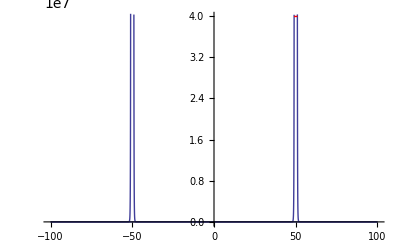

```mathematica
Rp=100;
a0=50;
r1=1;
r2=1;
c1=2;
c2=2;
ρ=0;
d1=Sqrt[a0^2+r1^2];
d2= -Sqrt[a0^2+r2^2];
omega = 1- z^2/Rp^2;
AAplot=omega^6 AA;
AAplot1=Simplify[AAplot/.z->(d1+r1)];
AAplot2=Simplify[AAplot/.z->(d2-r1)];
plot0=Plot[0,{z,-Rp,Rp},PlotRange-> {0,Max[AAplot1,AAplot2]}];
plot1=Plot[AAplot,{z,0,Rp},RegionFunction->Function[{z},(z-Sqrt[a0^2+r1^2])^2≥ r1^2],PlotRange->Full];
plot2=Plot[AAplot,{z,-Rp,0},RegionFunction->Function[{z},(z+Sqrt[a0^2+r2^2])^2≥ r2^2],PlotRange->Full];
plot3=Plot[(AAplot1),{z,-Rp,Rp},RegionFunction->Function[{z},(z-Sqrt[a0^2+r1^2])^2≤  r1^2],PlotStyle->Red];
plot4=Plot[(AAplot2),{z,-Rp,Rp},RegionFunction->Function[{z},(z+Sqrt[a0^2+r2^2])^2≤  r2^2],PlotStyle->Red];
Show[{plot0,plot1,plot2,plot3,plot4}]
```

### Add in Kugelkoordinaten

```mathematica
alt={x,y,z};
neu={ρ,z,φ};
dim3=3;
x=ρ Sin[φ];
y=ρ Cos[φ];
z=z;
T=Table[D[alt[[i]],neu[[j]]],{i,1,dim3},{j,1,dim3}];
Su={0,0,Sz};
Pu={0,0,Pz};
R=Sqrt[x^2+y^2+(z-d)^2];
ϵ=LeviCivitaTensor[dim3];
Acdd=FullSimplify[Table[c/(R)^3 (3 alt[[i]] alt[[j]]/R^2-KroneckerDelta[i,j]),{i,1,dim3},{j,1,dim3}]];
ASdd=Table[(-3/R^3 )(Sum[ϵ[[i,k,l]]Su[[k]]alt[[l]] alt[[j]]/R^2,{k,1,dim3},{l,1,dim3}] + Sum[ϵ[[j,k,l]]Su[[k]]alt[[l]] alt[[i]]/R^2,{k,1,dim3},{l,1,dim3}]),{i,1,dim3},{j,1,dim3}];
APdd = Table[-3/(2 R^3 )(Pu[[i]] alt[[j]]/R +Pu[[j]] alt[[i]]/R  + Sum[Pu[[k]]alt[[k]]/R,{k,1,dim3}]( alt[[i]] alt[[j]]/R^2-KroneckerDelta[i,j])),{i,1,dim3},{j,1,dim3}];
A1dd=Acdd + ASdd + APdd;
Clear[R]
A2dd=Simplify[Table[Sum[T[[i1,i2]] T[[j1,j2]] A1dd[[i1,j1]],{i1,1,dim3},{j1,1,dim3}],{i2,1,dim3},{j2,1,dim3}]];
```

```mathematica
Clear[alt,neu,ρ,z,T]
alt={ρ,z,φ};
neu={R,μ,φ};
ρ = R Sqrt[1-μ^2];
z=R μ + dd;
T=Table[D[alt[[i]],neu[[j]]],{i,1,dim3},{j,1,dim3}];
A3dd=FullSimplify[Table[Sum[T[[i1,i2]] T[[j1,j2]] A2dd[[i1,j1]],{i1,1,dim3},{j1,1,dim3}],{i2,1,dim3},{j2,1,dim3}]];
```

```mathematica
Add=((A3dd/.c->c1/.d->d1/.Sz->Sz1/.Pz->Pz1) + (A3dd/.c->c2/.d->d2/.Sz->Sz2/.Pz->Pz2))/.dd->d;
```

```mathematica
CForm[Add[[2,2]]/.μ->mu]/.Power->pow
```

(pow(R,2)*pow(-1 + pow(mu,2),-1)*
      pow((-d + d1)*(-d + d1 - 2*mu*R) + pow(R,2),-3.5)*
      (2*c1*((-d + d1)*(-d + d1 - 2*mu*R) + pow(R,2))*
         (2*d*mu*R - 2*d1*(d + mu*R) + pow(d1,2) + pow(d,2)*(-2 + 3*pow(mu,2)) + 
           pow(R,2)) - 3*Pz1*(pow(d,3)*(-2 + 3*pow(mu,2)) + 
           mu*R*pow(d,2)*(-2 + 5*pow(mu,2)) - 
           2*d1*(d + mu*R)*(mu*R + d*(-1 + 2*pow(mu,2))) + 
           pow(d1,2)*(mu*R + d*(-1 + 2*pow(mu,2))) + 
           d*(-1 + 4*pow(mu,2))*pow(R,2) + mu*pow(R,3))*
         pow((-d + d1)*(-d + d1 - 2*mu*R) + pow(R,2),0.5)))/2. + 
   (pow(R,2)*pow(-1 + pow(mu,2),-1)*
      pow((-d + d2)*(-d + d2 - 2*mu*R) + pow(R,2),-3.5)*
      (2*c2*((-d + d2)*(-d + d2 - 2*mu*R) + pow(R,2))*
         (2*d*mu*R - 2*d2*(d + mu*R) + pow(d2,2) + pow(d,2)*(-2 + 3*pow(mu,2)) + 
           pow(R,2)) - 3*Pz2*(pow(d,3)*(-2 + 3*pow(mu,2)) + 
           mu*R*pow(d,2)*(-2 + 5*pow(mu,2)) - 
           2*d2*(d + mu*R)*(mu*R + d*(-1 + 2*pow(mu,2))) + 
           pow(d2,2)*(mu*R + d*(-1 + 2*pow(mu,2))) + 
           d*(-1 + 4*pow(mu,2))*pow(R,2) + mu*pow(R,3))*
         pow((-d + d2)*(-d + d2 - 2*mu*R) + pow(R,2),0.5)))/2.

```mathematica
Add[[2,2]]
```

(R^2 (2 c1 (R^2+(-d+d1) (-d+d1-2 R μ)) (d1^2+R^2+2 d R μ-2 d1 (d+R μ)+d^2 (-2+3 μ^2))-3 Pz1 √(R^2+(-d+d1) (-d+d1-2 R μ)) (R^3 μ+d^3 (-2+3 μ^2)+d R^2 (-1+4 μ^2)+d^2 R μ (-2+5 μ^2)+d1^2 (R μ+d (-1+2 μ^2))-2 d1 (d+R μ) (R μ+d (-1+2 μ^2)))))/(2 (-1+μ^2) (R^2+(-d+d1) (-d+d1-2 R μ))^(7/2))+(R^2 (2 c2 (R^2+(-d+d2) (-d+d2-2 R μ)) (d2^2+R^2+2 d R μ-2 d2 (d+R μ)+d^2 (-2+3 μ^2))-3 Pz2 √(R^2+(-d+d2) (-d+d2-2 R μ)) (R^3 μ+d^3 (-2+3 μ^2)+d R^2 (-1+4 μ^2)+d^2 R μ (-2+5 μ^2)+d2^2 (R μ+d (-1+2 μ^2))-2 d2 (d+R μ) (R μ+d (-1+2 μ^2)))))/(2 (-1+μ^2) (R^2+(-d+d2) (-d+d2-2 R μ))^(7/2))

```mathematica
Add3=Table[Add[[3,i]],{i,1,dim3}]
```

{-(3 R^2 Sz1 (R+d μ) (-1+μ^2))/((R^2+(-d+d1) (-d+d1-2 R μ))^(5/2))-(3 R^2 Sz2 (R+d μ) (-1+μ^2))/((R^2+(-d+d2) (-d+d2-2 R μ))^(5/2)),-(3 d R^3 Sz1 (-1+μ^2))/((R^2+(-d+d1) (-d+d1-2 R μ))^(5/2))-(3 d R^3 Sz2 (-1+μ^2))/((R^2+(-d+d2) (-d+d2-2 R μ))^(5/2)),1/2 R^2 (1-μ^2) ((3 Pz1 (d+R μ))/((R^2+(-d+d1) (-d+d1-2 R μ))^2)-(2 c1)/((R^2+(-d+d1) (-d+d1-2 R μ))^(3/2)))+1/2 R^2 (1-μ^2) ((3 Pz2 (d+R μ))/((R^2+(-d+d2) (-d+d2-2 R μ))^2)-(2 c2)/((R^2+(-d+d2) (-d+d2-2 R μ))^(3/2)))}